# Bidiakis Cube

### Author

Eric W. Weisstein
May 29, 2007

This notebook downloaded from http://mathworld.wolfram.com/notebooks/GraphTheory/BidiakisCube.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/BidiakisCube.html.

©2007 Wolfram Research, Inc. except for portions noted otherwise

## Canonical Name

```mathematica
GraphData["BidiakisCube","StandardName"]
```

{CubicPolyhedral,4}

## Embeddings

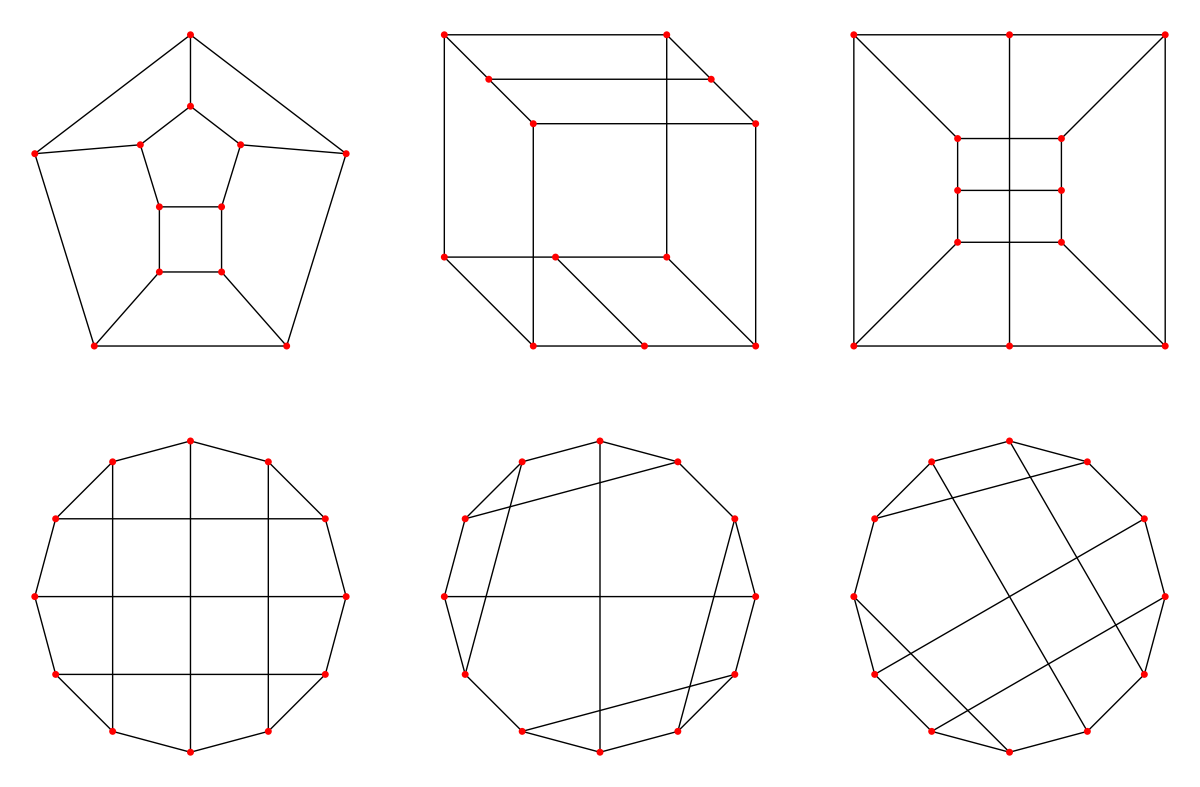

```mathematica
GraphicsGrid[Partition[GraphData["BidiakisCube","AllImages"],3,3,{1,1},{}]]
```

### LCF

```mathematica
"LCF"/.GraphData["BidiakisCube","NotationRules"]
```

{{{-6,4,-4},4},{{-6,-3,3,-6,3,-3},2},{{-6,-3,3,-6,4,-3,-6,4,-4,-6,3,-4},1}}

## GraphData

```mathematica
GraphClassString["BidiakisCube"]
```

\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Biconnected Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Class 1 Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Connected Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Cubic Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Hamiltonian Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:LCF Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Perfect Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Planar Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Polyhedral Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Regular Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Traceable Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Triangle-Free Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Weakly Regular Graphs}

## Construction

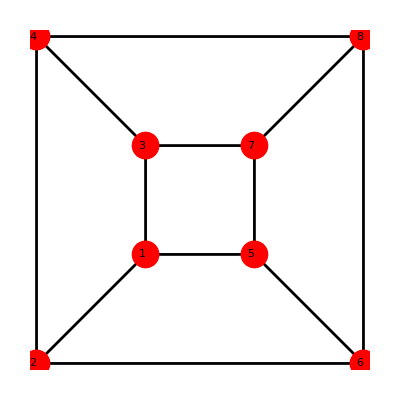

```mathematica
ShowLabeledGraph[g=Graph["CubicalGraph"]]
```

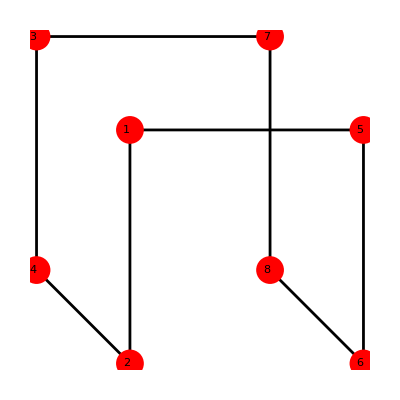

```mathematica
With[{d=.4},(g2=DeleteEdges[ChangeVertices[g,{{0,1},{0,0},{-d,1+d},{-d,d},{1,1},{1,0},{-d+1,1+d},{-d+1,d}}],{{2,6},{4,8},{1,3},{5,7}}])
]//ShowLabeledGraph
```

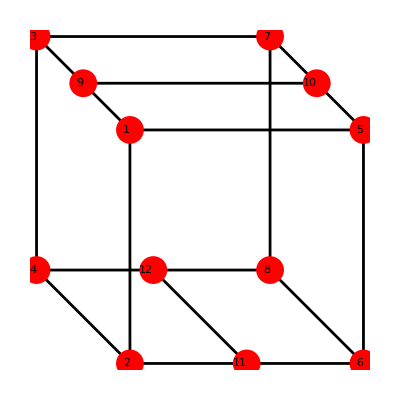

```mathematica
v=Vertices[g2];
(g3=AddEdges[AddVertices[g2,Mean[v[[#]]]&/@{{1,3},{5,7},{2,6},{4,8}}],{{1,9},{3,9},{5,10},{7,10},{4,12},{8,12},{2,11},{6,11},{11,12},{9,10}}])//ShowLabeledGraph
```

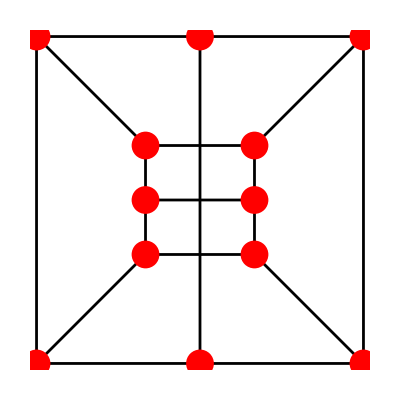

```mathematica
(g4=ChangeVertices[g3,{{1/3,1/3},{0,0},{1/3,2/3},{0,1},{2/3,1/3},{1,0},{2/3,2/3},{1,1},{1/3,1/2},{2/3,1/2},{1/2,0},{1/2,1}}])//ShowGraph
```

```mathematica
RecognizeGraph[g3]
```

{CubicPolyhedral,4}

```mathematica
ToCommonEdges[#,Graph[{"CubicPolyhedral",4}]]&/@{g3,g4}
```

{{{0,1},{0,0},{1,1},{1/2,0},{1,0},{0.8,1.2},{-0.2,1.2},{0.1,0.4},{0.6,0.4},{0.6,1.4},{-0.4,0.4},{-0.4,1.4}},{{1/3,1/3},{0,0},{2/3,1/3},{1/2,0},{1,0},{2/3,1/2},{1/3,1/2},{1/2,1},{1,1},{2/3,2/3},{0,1},{1/3,2/3}}}